{0,0,10,12,30,24,20,18,19,15,0,0,0,2}

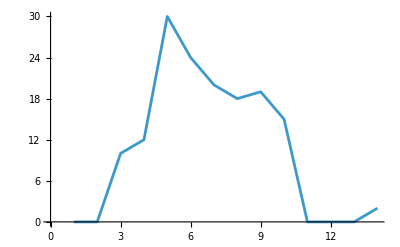

```mathematica
l1={0,0,10,12,30,24,20,18,19,15,0,0,0,2}
ListLinePlot[l1]
```

```mathematica
cwt12=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{2,4}]
```

ContinuousWaveletData[…]

```mathematica
cwt14=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{4,4}]
```

ContinuousWaveletData[…]

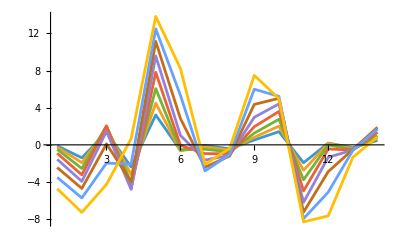

```mathematica
ListLinePlot[cwt12[All,"Values"]//Re,PlotRange->Full]
```

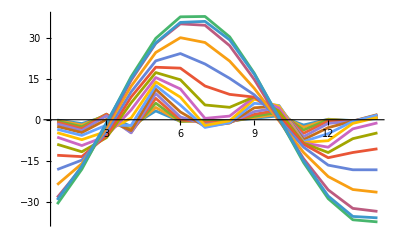

```mathematica
ListLinePlot[cwt14[All,"Values"]//Re,PlotRange->Full]
```

```mathematica
cwt12[All,"Values"][[8]]
```

{-4.72526-3.70159×10^-16 ⅈ,-7.26974-1.37372×10^-16 ⅈ,-4.26282-2.43198×10^-16 ⅈ,0.660352-1.96943×10^-16 ⅈ,13.8243+2.36327×10^-16 ⅈ,8.23601-6.83386×10^-17 ⅈ,-2.09672+2.59215×10^-16 ⅈ,-0.37624+2.97255×10^-16 ⅈ,7.47942+6.08131×10^-17 ⅈ,4.97986+2.97255×10^-16 ⅈ,-8.29551+1.26222×10^-16 ⅈ,-7.65297-6.83386×10^-17 ⅈ,-1.33551+4.20477×10^-18 ⅈ,0.834854-1.96943×10^-16 ⅈ}

```mathematica
cwt14[All,"Values"][[8]]
```

{-4.72526-3.70159×10^-16 ⅈ,-7.26974-1.37372×10^-16 ⅈ,-4.26282-2.43198×10^-16 ⅈ,0.660352-1.96943×10^-16 ⅈ,13.8243+2.36327×10^-16 ⅈ,8.23601-6.83386×10^-17 ⅈ,-2.09672+2.59215×10^-16 ⅈ,-0.37624+2.97255×10^-16 ⅈ,7.47942+6.08131×10^-17 ⅈ,4.97986+2.97255×10^-16 ⅈ,-8.29551+1.26222×10^-16 ⅈ,-7.65297-6.83386×10^-17 ⅈ,-1.33551+4.20477×10^-18 ⅈ,0.834854-1.96943×10^-16 ⅈ}

{0,0,10,12,30,40,60,100,110,111}

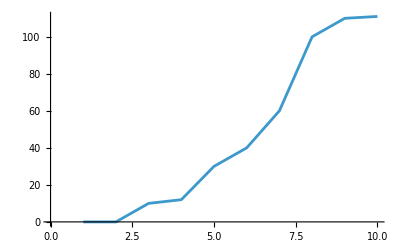

```mathematica
l2={0,0,10,12,30,40,60,100,110,111}
ListLinePlot[l2]
```

```mathematica
cwt2=ContinuousWaveletTransform[l2,MexicanHatWavelet[1],{3,4}]
```

ContinuousWaveletData[…]

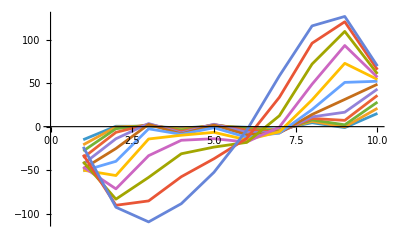

```mathematica
ListLinePlot[cwt2[All,"Values"]]
```

{0.51952,0.390202,0.0833617,0.410318,0.198675,0.145551,0.562975,0.214298,0.6591,0.605698}

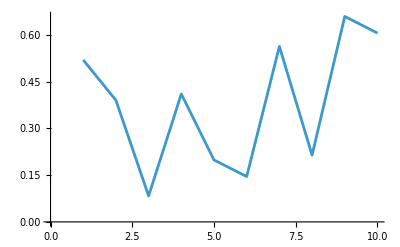

```mathematica
lr=Table[RandomReal[],{10}]
ListLinePlot[lr]
```

```mathematica
cwtr=ContinuousWaveletTransform[lr,MexicanHatWavelet[1]]
```

ContinuousWaveletData[…]

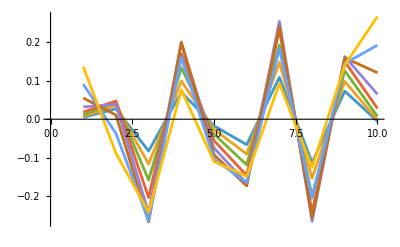

```mathematica
ListLinePlot[cwtr[All,"Values"]]
```

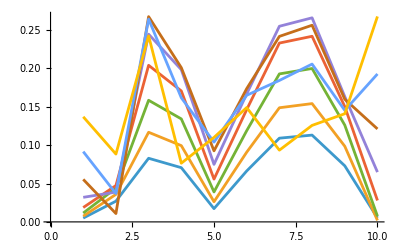

```mathematica
Map[Abs,cwtr[All,"Values"]]//ListLinePlot
```

```mathematica
Map[Norm,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

```mathematica
Map[Re,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

ピーク推定

モジュール読み込み：

```mathematica
Get["/Users/kouamano/gitsrc/SCRIPT_Mathematica/SCRIPTS/Wavelet.txt"]
```

Get::noopen: /Users/kouamano/gitsrc/SCRIPT_Mathematica/SCRIPTS/Wavelet.txtを開くことができません．

$Failed

```mathematica
cwtr[All,"Values"]
```

{{0.00497057-1.87546×10^-18 ⅈ,0.0270116+2.56935×10^-18 ⅈ,-0.082939-2.69118×10^-18 ⅈ,0.0706779+1.31409×10^-18 ⅈ,-0.0172904-5.55605×10^-19 ⅈ,-0.066378+2.08988×10^-18 ⅈ,0.109149-3.19532×10^-18 ⅈ,-0.113145+2.08988×10^-18 ⅈ,0.0731295-1.05975×10^-18 ⅈ,-0.0051859+1.31409×10^-18 ⅈ},{0.007449-1.35108×10^-17 ⅈ,0.0358724-3.67036×10^-19 ⅈ,-0.116855-5.8393×10^-18 ⅈ,0.0994235+9.00651×10^-18 ⅈ,-0.0262816+6.57337×10^-18 ⅈ,-0.0908753+1.42829×10^-17 ⅈ,0.148805+6.57337×10^-18 ⅈ,-0.154217+1.23144×10^-18 ⅈ,0.0986347-5.8393×10^-18 ⅈ,-0.00195586-1.21112×10^-17 ⅈ},{0.0115191-2.86723×10^-18 ⅈ,0.0440821+5.64279×10^-18 ⅈ,-0.158558-6.13009×10^-18 ⅈ,0.134262+6.21758×10^-19 ⅈ,-0.0390455+2.41219×10^-18 ⅈ,-0.118876+3.72493×10^-18 ⅈ,0.192937-8.14666×10^-18 ⅈ,-0.199982+3.72493×10^-18 ⅈ,0.126183+3.95633×10^-19 ⅈ,0.00747747+6.21758×10^-19 ⅈ},{0.0187379-3.06623×10^-18 ⅈ,0.0474108-5.26045×10^-18 ⅈ,-0.204133-4.69766×10^-18 ⅈ,0.170727+7.94882×10^-18 ⅈ,-0.0557807-4.26513×10^-19 ⅈ,-0.146393+1.94315×10^-17 ⅈ,0.233131-5.70594×10^-18 ⅈ,-0.241973+6.38009×10^-18 ⅈ,0.150314-1.43479×10^-18 ⅈ,0.0279592-1.31689×10^-17 ⅈ},{0.0320215-2.50221×10^-17 ⅈ,0.0388476+8.36875×10^-18 ⅈ,-0.244685-9.67919×10^-18 ⅈ,0.198474-1.67331×10^-18 ⅈ,-0.0749791+1.51462×10^-17 ⅈ,-0.166912+4.53302×10^-18 ⅈ,0.25503+1.51462×10^-17 ⅈ,-0.266047+4.53302×10^-18 ⅈ,0.163347-9.67919×10^-18 ⅈ,0.0649026-1.67331×10^-18 ⅈ},{0.0554397-2.08941×10^-18 ⅈ,0.0108914+7.64052×10^-18 ⅈ,-0.267617-8.61514×10^-18 ⅈ,0.201064-2.40154×10^-18 ⅈ,-0.092629+8.46944×10^-18 ⅈ,-0.173722+3.8048×10^-18 ⅈ,0.241835-1.26483×10^-17 ⅈ,-0.256374+3.8048×10^-18 ⅈ,0.159918+4.43632×10^-18 ⅈ,0.121194-2.40154×10^-18 ⅈ},{0.0916354,-0.0369275,-0.26437,0.161825,-0.104009,-0.16508,0.184409,-0.205746,0.145417,0.192848},{0.137028,-0.088428,-0.24247,0.0765112,-0.110153,-0.149032,0.0935189,-0.125799,0.141002,0.267821}}

```mathematica
WTPE[cwtr[All,"Values"]]
```

WTPE[{{0.00497057-1.87546×10^-18 ⅈ,0.0270116+2.56935×10^-18 ⅈ,-0.082939-2.69118×10^-18 ⅈ,0.0706779+1.31409×10^-18 ⅈ,-0.0172904-5.55605×10^-19 ⅈ,-0.066378+2.08988×10^-18 ⅈ,0.109149-3.19532×10^-18 ⅈ,-0.113145+2.08988×10^-18 ⅈ,0.0731295-1.05975×10^-18 ⅈ,-0.0051859+1.31409×10^-18 ⅈ},{0.007449-1.35108×10^-17 ⅈ,0.0358724-3.67036×10^-19 ⅈ,-0.116855-5.8393×10^-18 ⅈ,0.0994235+9.00651×10^-18 ⅈ,-0.0262816+6.57337×10^-18 ⅈ,-0.0908753+1.42829×10^-17 ⅈ,0.148805+6.57337×10^-18 ⅈ,-0.154217+1.23144×10^-18 ⅈ,0.0986347-5.8393×10^-18 ⅈ,-0.00195586-1.21112×10^-17 ⅈ},{0.0115191-2.86723×10^-18 ⅈ,0.0440821+5.64279×10^-18 ⅈ,-0.158558-6.13009×10^-18 ⅈ,0.134262+6.21758×10^-19 ⅈ,-0.0390455+2.41219×10^-18 ⅈ,-0.118876+3.72493×10^-18 ⅈ,0.192937-8.14666×10^-18 ⅈ,-0.199982+3.72493×10^-18 ⅈ,0.126183+3.95633×10^-19 ⅈ,0.00747747+6.21758×10^-19 ⅈ},{0.0187379-3.06623×10^-18 ⅈ,0.0474108-5.26045×10^-18 ⅈ,-0.204133-4.69766×10^-18 ⅈ,0.170727+7.94882×10^-18 ⅈ,-0.0557807-4.26513×10^-19 ⅈ,-0.146393+1.94315×10^-17 ⅈ,0.233131-5.70594×10^-18 ⅈ,-0.241973+6.38009×10^-18 ⅈ,0.150314-1.43479×10^-18 ⅈ,0.0279592-1.31689×10^-17 ⅈ},{0.0320215-2.50221×10^-17 ⅈ,0.0388476+8.36875×10^-18 ⅈ,-0.244685-9.67919×10^-18 ⅈ,0.198474-1.67331×10^-18 ⅈ,-0.0749791+1.51462×10^-17 ⅈ,-0.166912+4.53302×10^-18 ⅈ,0.25503+1.51462×10^-17 ⅈ,-0.266047+4.53302×10^-18 ⅈ,0.163347-9.67919×10^-18 ⅈ,0.0649026-1.67331×10^-18 ⅈ},{0.0554397-2.08941×10^-18 ⅈ,0.0108914+7.64052×10^-18 ⅈ,-0.267617-8.61514×10^-18 ⅈ,0.201064-2.40154×10^-18 ⅈ,-0.092629+8.46944×10^-18 ⅈ,-0.173722+3.8048×10^-18 ⅈ,0.241835-1.26483×10^-17 ⅈ,-0.256374+3.8048×10^-18 ⅈ,0.159918+4.43632×10^-18 ⅈ,0.121194-2.40154×10^-18 ⅈ},{0.0916354,-0.0369275,-0.26437,0.161825,-0.104009,-0.16508,0.184409,-0.205746,0.145417,0.192848},{0.137028,-0.088428,-0.24247,0.0765112,-0.110153,-0.149032,0.0935189,-0.125799,0.141002,0.267821}}]

```mathematica
cwt2[All,"Values"]//WTPE
```

WTPE[{{-15.0158+3.50454×10^-16 ⅈ,0.465471+5.37724×10^-16 ⅈ,0.487579-5.97047×10^-16 ⅈ,-1.66076+8.87437×10^-16 ⅈ,0.792816+6.83045×10^-17 ⅈ,-0.676056-1.04168×10^-16 ⅈ,-3.09651-3.49342×10^-16 ⅈ,4.5449+9.3413×10^-16 ⅈ,-1.07434-1.27281×10^-15 ⅈ,15.2327-4.54681×10^-16 ⅈ},{-20.8956+6.03378×10^-16 ⅈ,-0.347541+6.40072×10^-16 ⅈ,0.988663-1.3247×10^-15 ⅈ,-2.57689+9.45196×10^-16 ⅈ,1.25093-1.33082×10^-16 ⅈ,-1.3049-4.96321×10^-16 ⅈ,-4.1019-1.33082×10^-16 ⅈ,6.07088+1.53098×10^-15 ⅈ,-0.237792-1.3247×10^-15 ⅈ,21.1541-3.07744×10^-16 ⅈ},{-28.0068+8.70577×10^-16 ⅈ,-2.38166+5.50508×10^-16 ⅈ,1.79792-2.53548×10^-15 ⅈ,-3.87801+1.3858×10^-15 ⅈ,1.86747+1.24016×10^-15 ⅈ,-2.39254-8.01024×10^-16 ⅈ,-5.16001-1.4629×10^-15 ⅈ,7.74858+1.90204×10^-15 ⅈ,2.12612-8.64898×10^-16 ⅈ,28.2789-2.84785×10^-16 ⅈ},{-35.7707+1.54291×10^-15 ⅈ,-6.55421+5.88715×10^-16 ⅈ,2.84227-3.14853×10^-15 ⅈ,-5.52763+1.84165×10^-15 ⅈ,2.51153+1.42153×10^-15 ⅈ,-4.1049-1.43858×10^-15 ⅈ,-6.11225-1.28154×10^-15 ⅈ,9.45007+2.61601×10^-15 ⅈ,7.25399-1.47795×10^-15 ⅈ,36.0119-6.64224×10^-16 ⅈ},{-43.0666+2.30119×10^-15 ⅈ,-13.9206+1.85714×10^-16 ⅈ,3.58798-2.84035×10^-15 ⅈ,-7.23467+2.49899×10^-15 ⅈ,2.76196+3.37294×10^-16 ⅈ,-6.48556-2.27186×10^-15 ⅈ,-6.82049+3.37294×10^-16 ⅈ,11.2725+3.13427×10^-15 ⅈ,16.6355-2.84035×10^-15 ⅈ,43.2701-8.4218×10^-16 ⅈ},{-48.4743+2.441×10^-15 ⅈ,-25.1683-3.09376×10^-16 ⅈ,2.62006-1.349×10^-15 ⅈ,-8.43493+2.64659×10^-15 ⅈ,1.82042+1.31241×10^-15 ⅈ,-9.3319-2.52147×10^-15 ⅈ,-7.25895-3.5818×10^-16 ⅈ,14.033+2.88466×10^-15 ⅈ,31.3438-4.05206×10^-15 ⅈ,48.851-6.94579×10^-16 ⅈ},{-50.8974+2.62252×10^-15 ⅈ,-39.891-6.68523×10^-16 ⅈ,-2.46578-2.51902×10^-15 ⅈ,-8.84857+2.60879×10^-15 ⅈ,-1.19825+6.58624×10^-16 ⅈ,-12.2864-2.75787×10^-15 ⅈ,-7.3152+6.58624×10^-16 ⅈ,19.6924+2.64826×10^-15 ⅈ,50.9538-2.51902×10^-15 ⅈ,52.2564-7.32379×10^-16 ⅈ},{-50.0968+2.76385×10^-15 ⅈ,-56.2547+6.11228×10^-16 ⅈ,-14.1775-2.37769×10^-15 ⅈ,-9.8851+2.98836×10^-15 ⅈ,-6.55583+7.99959×10^-16 ⅈ,-15.1731-5.16313×10^-15 ⅈ,-5.96285+7.99959×10^-16 ⅈ,30.857+5.64913×10^-15 ⅈ,72.8983-2.37769×10^-15 ⅈ,54.3506-3.69398×10^-15 ⅈ},{-46.4688+2.82695×10^-15 ⅈ,-71.592+1.43631×10^-15 ⅈ,-33.3888-1.63882×10^-15 ⅈ,-15.6731-1.13446×10^-15 ⅈ,-13.8466+1.2807×10^-15 ⅈ,-17.715+4.54365×10^-16 ⅈ,-0.458425+4.45407×10^-16 ⅈ,48.8893+4.54365×10^-16 ⅈ,93.4056-2.99036×10^-15 ⅈ,56.8478-1.13446×10^-15 ⅈ},{-40.3769,-83.4683,-58.3794,-31.1964,-23.5101,-18.1138,12.5713,72.0706,109.633,60.7704},{-32.2053,-90.4994,-85.47,-57.6367,-36.9133,-13.5188,33.8411,96.0703,120.746,65.5861},{-23.2367-1.35529×10^-22 ⅈ,-92.7565+1.35529×10^-22 ⅈ,-109.632+2.0273×10^-15 ⅈ,-88.663+5.40613×10^-15 ⅈ,-52.4895+1.25294×10^-15 ⅈ,-4.31509+3.34117×10^-15 ⅈ,58.5029-1.25294×10^-15 ⅈ,116.01-3.34117×10^-15 ⅈ,126.855-2.0273×10^-15 ⅈ,69.7251-5.40613×10^-15 ⅈ}}]

```mathematica
cwt[All,"Values"]//WTPE
```

WTPE[{{-0.107474-4.69358×10^-17 ⅈ,-1.39372+4.69358×10^-17 ⅈ,1.36457+7.55096×10^-18 ⅈ,-2.38144-5.09682×10^-17 ⅈ,3.21785+1.6149×10^-16 ⅈ,-0.589482-5.82428×10^-17 ⅈ,-0.0620502+3.8494×10^-17 ⅈ,-0.424957+6.36265×10^-17 ⅈ,0.521946-6.07068×10^-17 ⅈ,1.42439-4.14137×10^-17 ⅈ,-1.92725+1.06438×10^-16 ⅈ,0.189171-2.09685×10^-16 ⅈ,-0.304778+1.31252×10^-16 ⅈ,0.473219-8.78351×10^-17 ⅈ},{-0.238163-7.28794×10^-17 ⅈ,-1.91858+6.49492×10^-17 ⅈ,1.74389-3.17693×10^-17 ⅈ,-3.19399-1.44287×10^-16 ⅈ,4.49418+2.38448×10^-16 ⅈ,-0.64554-1.52165×10^-16 ⅈ,-0.198919+7.70799×10^-17 ⅈ,-0.581263+6.0577×10^-17 ⅈ,0.81186-1.21322×10^-16 ⅈ,2.01584-2.62238×10^-17 ⅈ,-2.73661+1.28343×10^-16 ⅈ,0.158072-2.00336×10^-16 ⅈ,-0.405195+2.15634×10^-16 ⅈ,0.694415-3.60481×10^-17 ⅈ},{-0.484197-1.08665×10^-16 ⅈ,-2.54282+1.48316×10^-16 ⅈ,2.03397-7.12369×10^-17 ⅈ,-4.03929-1.69526×10^-16 ⅈ,6.05804+3.20638×10^-16 ⅈ,-0.526331-2.53139×10^-16 ⅈ,-0.471686+1.08809×10^-16 ⅈ,-0.763581+1.01914×10^-16 ⅈ,1.26231-1.88793×10^-16 ⅈ,2.7562+2.75134×10^-17 ⅈ,-3.76306+1.55481×10^-16 ⅈ,-0.00544513-2.94429×10^-16 ⅈ,-0.503269+2.99867×10^-16 ⅈ,0.989156-7.67503×10^-17 ⅈ},{-0.907379-1.43199×10^-16 ⅈ,-3.22694+1.74919×10^-16 ⅈ,2.03216-5.72968×10^-17 ⅈ,-4.69133-7.47697×10^-17 ⅈ,7.8116+3.6148×10^-16 ⅈ,-0.0467163-1.66575×10^-16 ⅈ,-0.945425+8.92045×10^-17 ⅈ,-0.954178+1.65427×10^-16 ⅈ,1.95203-2.08398×10^-16 ⅈ,3.59573-6.67831×10^-18 ⅈ,-4.95796+1.96323×10^-16 ⅈ,-0.439206-4.48386×10^-16 ⅈ,-0.566122+3.13807×10^-16 ⅈ,1.34375-1.95858×10^-16 ⅈ},{-1.55975-2.13032×10^-16 ⅈ,-3.93204+3.08194×10^-16 ⅈ,1.46433-1.11423×10^-16 ⅈ,-4.79571+1.03208×10^-17 ⅈ,9.56901+4.39772×10^-16 ⅈ,1.02142-1.54239×10^-16 ⅈ,-1.6377+9.28575×10^-17 ⅈ,-1.12026+2.99781×10^-16 ⅈ,2.96923-3.03946×10^-16 ⅈ,4.41002+2.99718×10^-17 ⅈ,-6.18646+2.19563×10^-16 ⅈ,-1.33781-6.76571×10^-16 ⅈ,-0.558014+3.83383×10^-16 ⅈ,1.69373-3.24632×10^-16 ⅈ},{-2.44386-5.17244×10^-16 ⅈ,-4.69504+2.952×10^-16 ⅈ,0.108863-2.8131×10^-16 ⅈ,-3.97417-1.89133×10^-16 ⅈ,11.1374+5.06094×10^-16 ⅈ,2.84151-3.75858×10^-16 ⅈ,-2.40456+2.82989×10^-16 ⅈ,-1.20071+2.36982×10^-16 ⅈ,4.35616-1.13814×10^-16 ⅈ,5.00986+1.87382×10^-16 ⅈ,-7.24234+2.85884×10^-16 ⅈ,-2.88616-4.03384×10^-16 ⅈ,-0.500465+2.13496×10^-16 ⅈ,1.89356-1.27282×10^-16 ⅈ},{-3.50222,-5.71167,-1.97156,-2.06446,12.4836,5.35166,-2.80568,-1.05618,5.99055,5.22014,-7.94879,-5.09731,-0.597164,1.7091},{-4.72526-3.70159×10^-16 ⅈ,-7.26974-1.37372×10^-16 ⅈ,-4.26282-2.43198×10^-16 ⅈ,0.660352-1.96943×10^-16 ⅈ,13.8243+2.36327×10^-16 ⅈ,8.23601-6.83386×10^-17 ⅈ,-2.09672+2.59215×10^-16 ⅈ,-0.37624+2.97255×10^-16 ⅈ,7.47942+6.08131×10^-17 ⅈ,4.97986+2.97255×10^-16 ⅈ,-8.29551+1.26222×10^-16 ⅈ,-7.65297-6.83386×10^-17 ⅈ,-1.33551+4.20477×10^-18 ⅈ,0.834854-1.96943×10^-16 ⅈ},{-6.36452+2.03911×10^-18 ⅈ,-9.41725+6.32374×10^-16 ⅈ,-5.97775-1.21662×10^-16 ⅈ,3.58882+2.11467×10^-16 ⅈ,15.4131+5.70914×10^-17 ⅈ,11.2397-5.31748×10^-16 ⅈ,0.503864+1.0124×10^-16 ⅈ,1.33797-5.89504×10^-16 ⅈ,8.30702-9.71617×10^-17 ⅈ,4.30179-1.70893×10^-16 ⅈ,-8.43476-5.30132×10^-17 ⅈ,-10.0266+7.31626×10^-17 ⅈ,-3.33265+1.25741×10^-16 ⅈ,-1.13865+3.60867×10^-16 ⅈ},{-8.96743,-11.6875,-6.53585,6.18175,17.2289,14.5886,5.39229,4.53316,8.35046,3.13634,-8.54829,-11.9693,-6.91066,-4.79248},{-12.9731,-13.4683,-5.88453,8.27882,19.1636,18.8395,12.3137,9.25701,8.25939,1.56711,-8.92098,-13.865,-11.9578,-10.6094},{-18.1816,-14.7428,-4.49269,10.1493,21.4878,24.1624,20.3531,15.1154,9.09889,0.167265,-10.0001,-16.5769,-18.2655,-18.2747}}]

```mathematica
WTPE[cwt[All,"Values"],"position"]
```

WTPE[{{-0.107474-4.69358×10^-17 ⅈ,-1.39372+4.69358×10^-17 ⅈ,1.36457+7.55096×10^-18 ⅈ,-2.38144-5.09682×10^-17 ⅈ,3.21785+1.6149×10^-16 ⅈ,-0.589482-5.82428×10^-17 ⅈ,-0.0620502+3.8494×10^-17 ⅈ,-0.424957+6.36265×10^-17 ⅈ,0.521946-6.07068×10^-17 ⅈ,1.42439-4.14137×10^-17 ⅈ,-1.92725+1.06438×10^-16 ⅈ,0.189171-2.09685×10^-16 ⅈ,-0.304778+1.31252×10^-16 ⅈ,0.473219-8.78351×10^-17 ⅈ},{-0.238163-7.28794×10^-17 ⅈ,-1.91858+6.49492×10^-17 ⅈ,1.74389-3.17693×10^-17 ⅈ,-3.19399-1.44287×10^-16 ⅈ,4.49418+2.38448×10^-16 ⅈ,-0.64554-1.52165×10^-16 ⅈ,-0.198919+7.70799×10^-17 ⅈ,-0.581263+6.0577×10^-17 ⅈ,0.81186-1.21322×10^-16 ⅈ,2.01584-2.62238×10^-17 ⅈ,-2.73661+1.28343×10^-16 ⅈ,0.158072-2.00336×10^-16 ⅈ,-0.405195+2.15634×10^-16 ⅈ,0.694415-3.60481×10^-17 ⅈ},{-0.484197-1.08665×10^-16 ⅈ,-2.54282+1.48316×10^-16 ⅈ,2.03397-7.12369×10^-17 ⅈ,-4.03929-1.69526×10^-16 ⅈ,6.05804+3.20638×10^-16 ⅈ,-0.526331-2.53139×10^-16 ⅈ,-0.471686+1.08809×10^-16 ⅈ,-0.763581+1.01914×10^-16 ⅈ,1.26231-1.88793×10^-16 ⅈ,2.7562+2.75134×10^-17 ⅈ,-3.76306+1.55481×10^-16 ⅈ,-0.00544513-2.94429×10^-16 ⅈ,-0.503269+2.99867×10^-16 ⅈ,0.989156-7.67503×10^-17 ⅈ},{-0.907379-1.43199×10^-16 ⅈ,-3.22694+1.74919×10^-16 ⅈ,2.03216-5.72968×10^-17 ⅈ,-4.69133-7.47697×10^-17 ⅈ,7.8116+3.6148×10^-16 ⅈ,-0.0467163-1.66575×10^-16 ⅈ,-0.945425+8.92045×10^-17 ⅈ,-0.954178+1.65427×10^-16 ⅈ,1.95203-2.08398×10^-16 ⅈ,3.59573-6.67831×10^-18 ⅈ,-4.95796+1.96323×10^-16 ⅈ,-0.439206-4.48386×10^-16 ⅈ,-0.566122+3.13807×10^-16 ⅈ,1.34375-1.95858×10^-16 ⅈ},{-1.55975-2.13032×10^-16 ⅈ,-3.93204+3.08194×10^-16 ⅈ,1.46433-1.11423×10^-16 ⅈ,-4.79571+1.03208×10^-17 ⅈ,9.56901+4.39772×10^-16 ⅈ,1.02142-1.54239×10^-16 ⅈ,-1.6377+9.28575×10^-17 ⅈ,-1.12026+2.99781×10^-16 ⅈ,2.96923-3.03946×10^-16 ⅈ,4.41002+2.99718×10^-17 ⅈ,-6.18646+2.19563×10^-16 ⅈ,-1.33781-6.76571×10^-16 ⅈ,-0.558014+3.83383×10^-16 ⅈ,1.69373-3.24632×10^-16 ⅈ},{-2.44386-5.17244×10^-16 ⅈ,-4.69504+2.952×10^-16 ⅈ,0.108863-2.8131×10^-16 ⅈ,-3.97417-1.89133×10^-16 ⅈ,11.1374+5.06094×10^-16 ⅈ,2.84151-3.75858×10^-16 ⅈ,-2.40456+2.82989×10^-16 ⅈ,-1.20071+2.36982×10^-16 ⅈ,4.35616-1.13814×10^-16 ⅈ,5.00986+1.87382×10^-16 ⅈ,-7.24234+2.85884×10^-16 ⅈ,-2.88616-4.03384×10^-16 ⅈ,-0.500465+2.13496×10^-16 ⅈ,1.89356-1.27282×10^-16 ⅈ},{-3.50222,-5.71167,-1.97156,-2.06446,12.4836,5.35166,-2.80568,-1.05618,5.99055,5.22014,-7.94879,-5.09731,-0.597164,1.7091},{-4.72526-3.70159×10^-16 ⅈ,-7.26974-1.37372×10^-16 ⅈ,-4.26282-2.43198×10^-16 ⅈ,0.660352-1.96943×10^-16 ⅈ,13.8243+2.36327×10^-16 ⅈ,8.23601-6.83386×10^-17 ⅈ,-2.09672+2.59215×10^-16 ⅈ,-0.37624+2.97255×10^-16 ⅈ,7.47942+6.08131×10^-17 ⅈ,4.97986+2.97255×10^-16 ⅈ,-8.29551+1.26222×10^-16 ⅈ,-7.65297-6.83386×10^-17 ⅈ,-1.33551+4.20477×10^-18 ⅈ,0.834854-1.96943×10^-16 ⅈ},{-6.36452+2.03911×10^-18 ⅈ,-9.41725+6.32374×10^-16 ⅈ,-5.97775-1.21662×10^-16 ⅈ,3.58882+2.11467×10^-16 ⅈ,15.4131+5.70914×10^-17 ⅈ,11.2397-5.31748×10^-16 ⅈ,0.503864+1.0124×10^-16 ⅈ,1.33797-5.89504×10^-16 ⅈ,8.30702-9.71617×10^-17 ⅈ,4.30179-1.70893×10^-16 ⅈ,-8.43476-5.30132×10^-17 ⅈ,-10.0266+7.31626×10^-17 ⅈ,-3.33265+1.25741×10^-16 ⅈ,-1.13865+3.60867×10^-16 ⅈ},{-8.96743,-11.6875,-6.53585,6.18175,17.2289,14.5886,5.39229,4.53316,8.35046,3.13634,-8.54829,-11.9693,-6.91066,-4.79248},{-12.9731,-13.4683,-5.88453,8.27882,19.1636,18.8395,12.3137,9.25701,8.25939,1.56711,-8.92098,-13.865,-11.9578,-10.6094},{-18.1816,-14.7428,-4.49269,10.1493,21.4878,24.1624,20.3531,15.1154,9.09889,0.167265,-10.0001,-16.5769,-18.2655,-18.2747}},position]

```mathematica
WTPE[cwtr[All,"Values"],"position"]
```

WTPE[{{0.00497057-1.87546×10^-18 ⅈ,0.0270116+2.56935×10^-18 ⅈ,-0.082939-2.69118×10^-18 ⅈ,0.0706779+1.31409×10^-18 ⅈ,-0.0172904-5.55605×10^-19 ⅈ,-0.066378+2.08988×10^-18 ⅈ,0.109149-3.19532×10^-18 ⅈ,-0.113145+2.08988×10^-18 ⅈ,0.0731295-1.05975×10^-18 ⅈ,-0.0051859+1.31409×10^-18 ⅈ},{0.007449-1.35108×10^-17 ⅈ,0.0358724-3.67036×10^-19 ⅈ,-0.116855-5.8393×10^-18 ⅈ,0.0994235+9.00651×10^-18 ⅈ,-0.0262816+6.57337×10^-18 ⅈ,-0.0908753+1.42829×10^-17 ⅈ,0.148805+6.57337×10^-18 ⅈ,-0.154217+1.23144×10^-18 ⅈ,0.0986347-5.8393×10^-18 ⅈ,-0.00195586-1.21112×10^-17 ⅈ},{0.0115191-2.86723×10^-18 ⅈ,0.0440821+5.64279×10^-18 ⅈ,-0.158558-6.13009×10^-18 ⅈ,0.134262+6.21758×10^-19 ⅈ,-0.0390455+2.41219×10^-18 ⅈ,-0.118876+3.72493×10^-18 ⅈ,0.192937-8.14666×10^-18 ⅈ,-0.199982+3.72493×10^-18 ⅈ,0.126183+3.95633×10^-19 ⅈ,0.00747747+6.21758×10^-19 ⅈ},{0.0187379-3.06623×10^-18 ⅈ,0.0474108-5.26045×10^-18 ⅈ,-0.204133-4.69766×10^-18 ⅈ,0.170727+7.94882×10^-18 ⅈ,-0.0557807-4.26513×10^-19 ⅈ,-0.146393+1.94315×10^-17 ⅈ,0.233131-5.70594×10^-18 ⅈ,-0.241973+6.38009×10^-18 ⅈ,0.150314-1.43479×10^-18 ⅈ,0.0279592-1.31689×10^-17 ⅈ},{0.0320215-2.50221×10^-17 ⅈ,0.0388476+8.36875×10^-18 ⅈ,-0.244685-9.67919×10^-18 ⅈ,0.198474-1.67331×10^-18 ⅈ,-0.0749791+1.51462×10^-17 ⅈ,-0.166912+4.53302×10^-18 ⅈ,0.25503+1.51462×10^-17 ⅈ,-0.266047+4.53302×10^-18 ⅈ,0.163347-9.67919×10^-18 ⅈ,0.0649026-1.67331×10^-18 ⅈ},{0.0554397-2.08941×10^-18 ⅈ,0.0108914+7.64052×10^-18 ⅈ,-0.267617-8.61514×10^-18 ⅈ,0.201064-2.40154×10^-18 ⅈ,-0.092629+8.46944×10^-18 ⅈ,-0.173722+3.8048×10^-18 ⅈ,0.241835-1.26483×10^-17 ⅈ,-0.256374+3.8048×10^-18 ⅈ,0.159918+4.43632×10^-18 ⅈ,0.121194-2.40154×10^-18 ⅈ},{0.0916354,-0.0369275,-0.26437,0.161825,-0.104009,-0.16508,0.184409,-0.205746,0.145417,0.192848},{0.137028,-0.088428,-0.24247,0.0765112,-0.110153,-0.149032,0.0935189,-0.125799,0.141002,0.267821}},position]